Rechnung zu einem einzelnen Soliton

Rechnung für konstante und kosinusförmige effektive Geschwindigkeit

2N Solitonen, v = const. , ϵ = ϵ0 cos(π/2m)

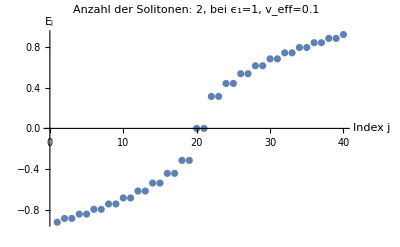

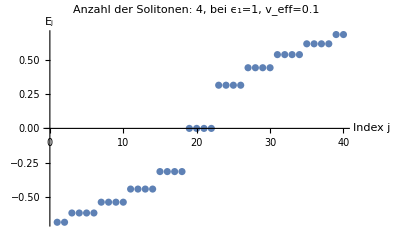

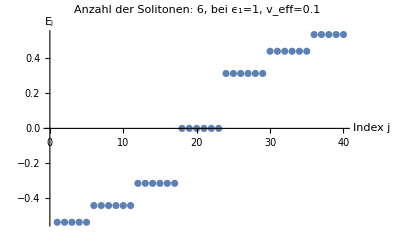

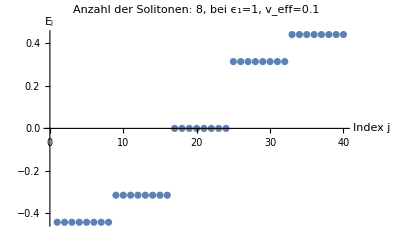

```mathematica
(*Parameter definieren*)
NSolitonenVconstMax=8;

ϵTestSingle=1;
vTestSingle=0.1;

Ntrunc=200;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)

dim=2*Ntrunc+1;
M=ConstantArray[0,{dim,dim}];


buildHMatrixVconst[Nmax_,m_,v_,em_,N_]:=Module[{dim,M,pos,n,posAn,posBn,posAnm,posBnm,posAnp,posBnp},dim=2*(2*Nmax+1);(*Dimension des Vektors*)M=ConstantArray[0,{dim,dim}];
(*Hilfsfunktion zur Indexberechnung*)pos[n_]:=2*(Nmax-n);
(*Position von a_n*)Do[posAn=pos[n]+1;(*1-basierte Position für a_n*)posBn=pos[n]+2;(*1-basierte Position für b_n*)
(*Erste Gleichung:v*n*b_n+(em/2)(a_{n-m}+a_{n+m})=E*a_n*)
M[[posAn,posBn]]=v/N(n+1/2);(*b_n-Term*)
(*a_{n-m} Term*)If[Abs[n-m]<=Nmax,posAnm=pos[n-m]+1;
M[[posAn,posAnm]]+=em/2;];
(*a_{n+m} Term*)If[Abs[n+m]<=Nmax,posAnp=pos[n+m]+1;
M[[posAn,posAnp]]+=em/2;];

(*Zweite Gleichung:v*n*a_n-(em/2)(b_{n-m}+b_{n+m})=E*b_n*)
M[[posBn,posAn]]=v/N(n+1/2);(*a_n-Term*)
(*b_{n-m} Term*)If[Abs[n-m]<=Nmax,posBnm=pos[n-m]+2;
M[[posBn,posBnm]]-=em/2;];
(*b_{n+m} Term*)If[Abs[n+m]<=Nmax,posBnp=pos[n+m]+2;
M[[posBn,posBnp]]-=em/2;],{n,-Nmax,Nmax}];
M];




For[i=1,(2i)<=NSolitonenVconstMax,i++,NSolitonen=2i;
M=ConstantArray[0,{dim,dim}];

M=buildHMatrixVconst[Ntrunc,NSolitonen/2,v,ϵ0,NSolitonen];


{NeigvalsSingle,NeigvecsSingle}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTestSingle}];
Print[ListPlot[Sort[NeigvalsSingle][[382;;421]],
PlotLabel->"Anzahl der Solitonen: "<>ToString[NSolitonen]<>", bei ϵ_1="<>ToString[ϵTestSingle]<>", v_eff="<> ToString[vTestSingle],AxesLabel->{"Index j","E_j"}](*[[380;;420]]*)]
]
```

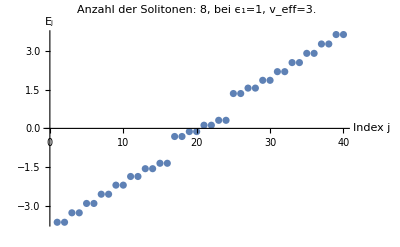

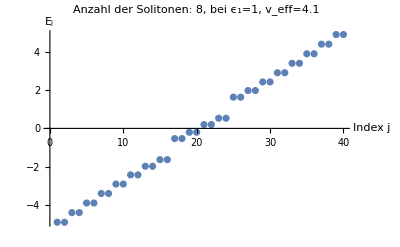

```mathematica
NSolitonen=8;

ϵTestSingle=1;
vTests={2.999,4.1};

Ntrunc=200;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)

dim=2*Ntrunc+1;
M=ConstantArray[0,{dim,dim}];
For[i=1,i<=Length[vTests],i++,
M=ConstantArray[0,{dim,dim}];

M=buildHMatrixVconst[Ntrunc,NSolitonen/2,v,ϵ0,NSolitonen];


{NeigvalsSingle,NeigvecsSingle}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTests[[i]]}];
Print[ListPlot[Sort[NeigvalsSingle][[382;;421]],
PlotLabel->"Anzahl der Solitonen: "<>ToString[NSolitonen]<>", bei ϵ_1="<>ToString[ϵTestSingle]<>", v_eff="<> ToString[Round[vTests[[i]],0.01]],AxesLabel->{"Index j","E_j"}](*[[380;;420]]*)]
]
```

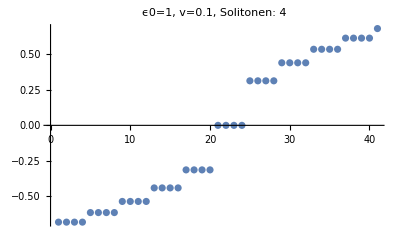

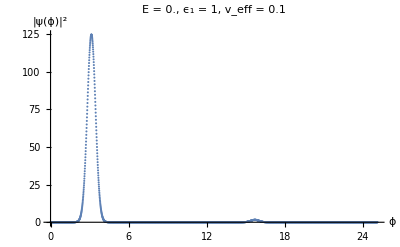

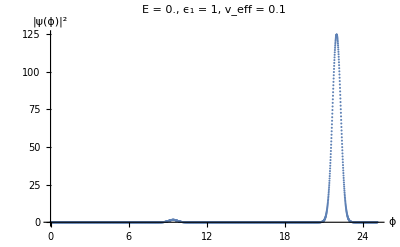

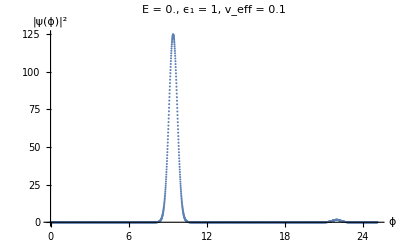

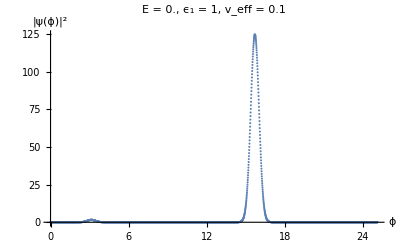

```mathematica
NSolitonen=4;
M=ConstantArray[0,{dim,dim}];
M=buildHMatrixVconst[Ntrunc,NSolitonen/2,v,ϵ0,NSolitonen];

ϵTestSingle=1;
vTestSingle=0.1;
{NeigvalsSingle1,NeigvecsSingle1}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTestSingle}];
{sortedNeigvalsSingle,sortedNeigvecsSingle}=Transpose[SortBy[Transpose[{NeigvalsSingle1,NeigvecsSingle1}],First]];
Print[ListPlot[Sort[NeigvalsSingle1][[380;;420]],
PlotLabel->"ϵ0="<>ToString[ϵTestSingle]<>", v="<> ToString[vTestSingle]<>", Solitonen: "<>ToString[NSolitonen]](*[[380;;420]]*)]
positions={400};

For[i=1,i<=Length[positions],i++,
pos=positions[[i]];
nValues=Range[-Ntrunc,Ntrunc];
vector1=E^(I*nValues/NSolitonen ϕ)*E^(I*ϕ/(2*NSolitonen));
ψ1=Total[sortedNeigvecsSingle[[pos]][[1;;-1;;2]]*vector1];
ψ2=Total[sortedNeigvecsSingle[[pos]][[2;;-1;;2]]*vector1];
ψ3=Total[sortedNeigvecsSingle[[pos+1]][[1;;-1;;2]]*vector1];
ψ4=Total[sortedNeigvecsSingle[[pos+1]][[2;;-1;;2]]*vector1];
ψ5=Total[sortedNeigvecsSingle[[pos+2]][[1;;-1;;2]]*vector1];
ψ6=Total[sortedNeigvecsSingle[[pos+2]][[2;;-1;;2]]*vector1];
ψ7=Total[sortedNeigvecsSingle[[pos+3]][[1;;-1;;2]]*vector1];
ψ8=Total[sortedNeigvecsSingle[[pos+3]][[2;;-1;;2]]*vector1];
phase1={-I,1,     I,1};
phase2={I,-1,     I ,1};
phase3={-1,I,     1,I};
phase4={1,-I,     1,I};


For[j=1,j<=Length[phase1],j++,
ψp={ψ1*phase1[[j]]+ψ3*phase2[[j]]+ψ5*phase3[[j]]+ψ7*phase4[[j]],    ψ2*phase1[[j]]+ψ4*phase2[[j]]+ψ6*phase3[[j]]+ψ8*phase4[[j]]};
ψ=Conjugate[ψp].ψp;
Print[ListPlot[

Table[{ϕ,Re[ψ]},{ϕ,0,2*NSolitonen*Pi,0.01}],
PlotRange->All,AxesLabel->{"ϕ","|ψ(ϕ)|^2"},PlotLabel->"E = "<>ToString[Round[sortedNeigvalsSingle[[pos]],0.001]]<>", ϵ_1 = "<>ToString[ϵTestSingle]<>", v_eff = "<>ToString[vTestSingle]]]
]]
```

2N Solitonen, v = v0 + v1 cos(π/2mv)  , ϵ = ϵ0 cos(π/2mϵ)

Matrix M erstellt. 2-Solitonen. Dimension: 401x401

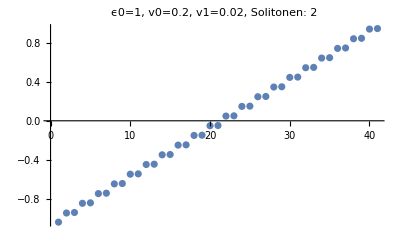

Matrix M erstellt. 4-Solitonen. Dimension: 401x401

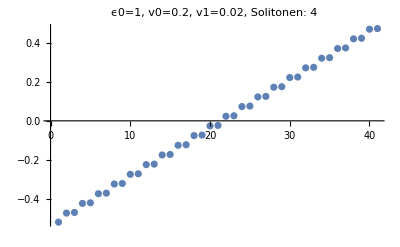

Matrix M erstellt. 6-Solitonen. Dimension: 401x401

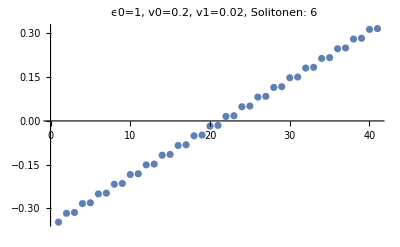

Matrix M erstellt. 8-Solitonen. Dimension: 401x401

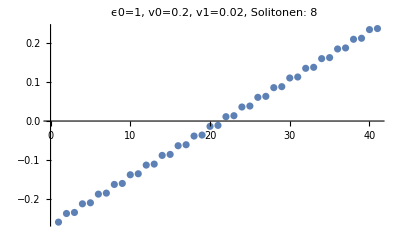

Matrix M erstellt. 10-Solitonen. Dimension: 401x401

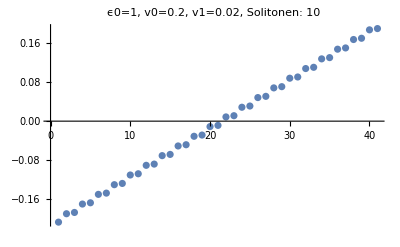

Matrix M erstellt. 12-Solitonen. Dimension: 401x401

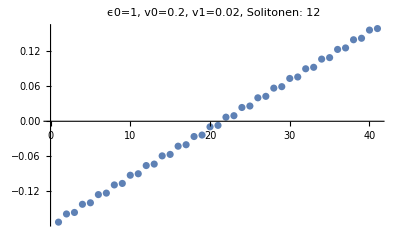

Matrix M erstellt. 14-Solitonen. Dimension: 401x401

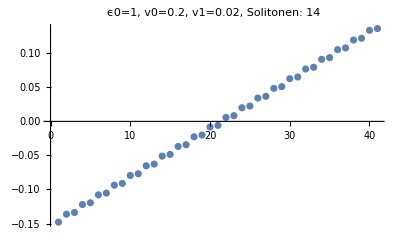

Matrix M erstellt. 16-Solitonen. Dimension: 401x401

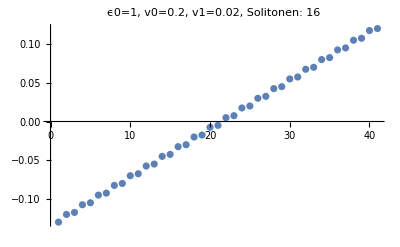

Matrix M erstellt. 18-Solitonen. Dimension: 401x401

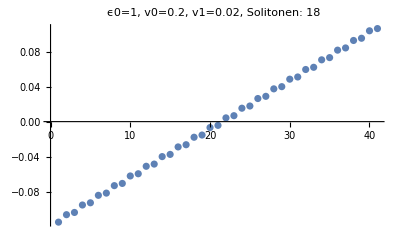

Matrix M erstellt. 20-Solitonen. Dimension: 401x401

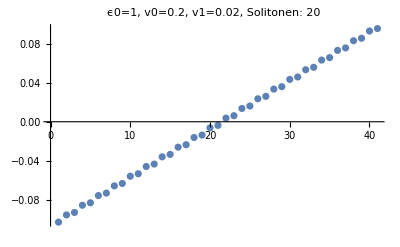

```mathematica
(*Parameter definieren*)
NSolitonenMax=20;

Ntrunc=200;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)

ϵ0TestSingle=1;
v0TestSingle=0.2;
v1TestSingle=0.02;




dim=2*Ntrunc+1;
M=ConstantArray[0,{dim,dim}];


buildHMatrix2N[Nmax_,m_,l_,v0_,v1_,e_,solitonen_]:=Module[{dim,M,pos,n,posAn,posBn,posAnm,posBnm,posAnp,posBnp,posAnlm,posAnlp,posBnlm,posBnlp},dim=2*(2*Nmax+1);(*Dimension des Vektors*)M=ConstantArray[0,{dim,dim}];
(*Hilfsfunktion zur Indexberechnung*)pos[n_]:=2*(Nmax-n);
Do[(*Positionen für a_n und b_n*)posAn=pos[n]+1;(*1-basierte Position für a_n*)posBn=pos[n]+2;(*1-basierte Position für b_n*)
(*Erste Gleichung:v0*n*a_n+v1*(n*m*b_{n-m}+n*m*b_{n+m})+e*(a_{n-l}+a_{n+l})=E*a_n*)
(*Diagonalelement für a_n*)M[[posAn,posAn]]=1/solitonen v0*(n+1/2);
(*b_{n-m} Term*)If[Abs[n-m]<=Nmax,posBnm=pos[n-m]+2;
M[[posAn,posBnm]]+=1/(2solitonen)v1*(n-m+m/2+1/2);];
(*b_{n+m} Term*)If[Abs[n+m]<=Nmax,posBnp=pos[n+m]+2;
M[[posAn,posBnp]]+=1/(2solitonen)v1*(n+m-m/2+1/2);];
(*a_{n-l} Term*)If[Abs[n-l]<=Nmax,posAnlm=pos[n-l]+1;
M[[posAn,posAnlm]]+=1/2 e;];
(*a_{n+l} Term*)If[Abs[n+l]<=Nmax,posAnlp=pos[n+l]+1;
M[[posAn,posAnlp]]+=1/2 e;];


(*Zweite Gleichung:v0*n*b_n+v1*(n*m*a_{n-m}+n*m*a_{n+m})-e*(b_{n-l}+b_{n+l})=E*b_n*)
(*Diagonalelement für b_n*)M[[posBn,posBn]]=1/solitonen v0*(n+1/2);
(*a_{n-m} Term*)If[Abs[n-m]<=Nmax,posAnm=pos[n-m]+1;
M[[posBn,posAnm]]+=1/(2solitonen)v1*(n-m+m/2+1/2);];
(*a_{n+m} Term*)If[Abs[n+m]<=Nmax,posAnp=pos[n+m]+1;
M[[posBn,posAnp]]+=1/(2solitonen)v1*(n+m-m/2+1/2);];
(*b_{n-l} Term*)If[Abs[n-l]<=Nmax,posBnlm=pos[n-l]+2;
M[[posBn,posBnlm]]-=1/2 e;];
(*b_{n+l} Term*)If[Abs[n+l]<=Nmax,posBnlp=pos[n+l]+2;
M[[posBn,posBnlp]]-=1/2 e;];,{n,-Nmax,Nmax}];
M];






For[i=1,(2i)<=NSolitonenMax,i++,NSolitonen=2i;

m=NSolitonen/2;(*v_ef- Terme*)
l=NSolitonen;(*ϵ - Terme*)

Mv=buildHMatrix2N[Ntrunc,m,l,v0,v1,ϵ0,NSolitonen];

Print["Matrix M erstellt. ", NSolitonen,"-Solitonen. Dimension: ",dim,"x",dim];
MatrixForm[Mv];
{NeigvalsSingle,NeigvecsSingle}=Eigensystem[Mv/.{ϵ0->ϵ0TestSingle,v0->v0TestSingle,v1->v1TestSingle}];
Print[ListPlot[Sort[NeigvalsSingle][[380;;420]],
PlotLabel->"ϵ0="<>ToString[ϵ0TestSingle]<>", v0="<> ToString[v0TestSingle]<>", v1="<> ToString[v1TestSingle]<>", Solitonen: "<>ToString[NSolitonen]]]
]
```